```mathematica
(****
TEMPLATE FOR ITERATIVE OPTIMIZATION ALGORITHMS
Zicheng Gao
 ****)
```

```mathematica
(*** Iteration Settings ***)
InitIterationSettings[]:=(
(* Controls - zero fps means that there is NO DELAY *)
doPrint=False;
doPoint=True;
doGraph=False;
doWarn=False;
doPlot=True;
doSpace=True;
doEPlot=True;

showMistakes=False;
fps=0;

(*Init*)
dir=gFunc@@iterParams;
err=eFunc@@iterParams;

(** Adaptivity **)
errorRatio=1.0;(*In what ratio of current error to previous error should it be considered increasing*)
boostRatio=1.1; (*'Impatience' Multiplier to increase factor when error is not increasing*)
refineRatio=0.95;(*'Caution' Multiplier to decrease factor when error is increasing*)
maxRefines=1000;(*Give up refining if refined too many times in a row*)
(* Acceleration *)
AccelBoost=1.;
AccelRefine=1.;
AccelAmt=0.01;

(* Tracker values *)
historyAmt=300;

(*Display*)
dispGradientRange=1.;
);
InitIterationSettings[];
```

```mathematica
InitFunctionData[paramVariance_,manualTrueParams_,noiseFactor_, noiseDistribution_,forceData_]:=(
Clear[eFunc,gFunc,params];
ParamVariance=paramVariance;

(*If we are forcing data, use data, otherwise generate data*)
If[Length[forceData]>0,
Data=forceData;
DataLength=Length[Data];
SamplingSet=N@Range@DataLength/N@SamplingRate;
(* Else *),
SamplingSet=N@Range@DataLength/N@SamplingRate;
TrueParams=If[Length[manualTrueParams]>0,manualTrueParams,RandomReal[{-paramVariance,paramVariance},varamt]];
(* Data Generation *)
NoiselessData=((Fitfunction@@ #&)/@(Prepend[TrueParams, #]& /@SamplingSet));
AddNoise=(#+noiseFactor*RandomVariate[noiseDistribution])&;
Data=AddNoise/@NoiselessData;
];

If[doNormalize,
DataMax=Max@Abs@Data;
Data/=DataMax,
DataMax=1];
(*Prep gradient*)
params=Table[Unique["p"],{varamt}];paramh=Hold@@params;

(* Objective and Gradient functions *)
eFunc=paramh/._[vars__]:>Function[{vars},N[Mean[(((Fitfunction@@Prepend[{vars},#])&/@SamplingSet)-Data)^2]]];
gFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[eFunc@@params,params]];
);
(*** Global Iteration Reset / Initialize ***)
InitIterationData[factorx_,manualParams_]:=(
totalIter=0;
TotalRefines=0;

(** Modification Values **)
factor=factorx;
dirs=ConstantArray[ConstantArray[0,varamt],Smoothness];
dirX=0;
err=-1;
prevErr=-2;
ConsecRefines=0;

(*History*)
iterParams=initParams=If[Length[manualParams]>0,manualParams,RandomReal[{-ParamVariance,ParamVariance},varamt]];
debugParams={iterParams};

err=eFunc@@iterParams;
dir=gFunc@@iterParams;
debugErr={err};
);
LinePlot[points_, size_,amount_]:=Show[
ListPointPlot3D[
{If[amount>0&&size>amount,points[[-amount;;-1]],points]},
PlotRange->All,ImageSize->Medium],
Graphics3D@Line@points
];
ReportIteration[i_]:=If[Mod[i,100]==0 && doPrint,Print["next dir:",dir,"\nerr:",err,"\nparams:",iterParams,"\niteration:",i];];
(* Realtime monitor plot *)
displayGradient[xV_,yV_]:=Show[
ContourPlot[eFunc @@ ReplacePart[iterParams, {xV->x,yV->y}],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
(* Realtime monitor plot *)
displayGradientNorm[xV_,yV_,ϵ_]:=Show[
ContourPlot[Norm[gFunc @@ ReplacePart[iterParams, {xV->x,yV->y}]],
{x,iterParams[[xV]]-dispGradientRange,iterParams[[xV]]+dispGradientRange},{y,iterParams[[yV]]-dispGradientRange,iterParams[[yV]]+dispGradientRange},
RegionFunction->Function[{x,y,z},z≤ϵ], PlotTheme->"Web",AxesLabel->{x,y,z},PlotRange->All,ImageSize->Small,PerformanceGoal->"Speed"
],
Graphics[{
Blue,PointSize[0.05],Point[{iterParams[[xV]],iterParams[[yV]]}],
Arrow[{{iterParams[[xV]],iterParams[[yV]]},{iterParams[[xV]]-factor*dir[[xV]],iterParams[[yV]]-factor*dir[[yV]]}}]
}]
];
Visualize[]:=Dynamic[Grid[{{"Data vs Function","Parameter Space","Error over iterations"},
{ListPlot[{DataMax*(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,DataMax*Data},Joined->True,ImageSize->Medium,PlotLegends->None]
,If[doPoint,If[varamt==3,If[doGraph,
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]},
LinePlot[debugParams,totalIter,historyAmt]],
"Non-3 dimensions"],
"Disabled"],
If[doEPlot,ListLogPlot[debugErr,ImageSize->Medium,PlotRange->All],"Disabled"]
},
{"Parameters, nGrad, dir, Delta","Iterations, factor, corrections"},{Column[{iterParams,-dir,-factor*dir,-factor*SmoothingFunction[dirs]}],Column[{{totalIter,factor,TotalRefines},ProgressIndicator[ConsecRefines/maxRefines]}],{(Total[(((Fitfunction@@Prepend[iterParams,#])&/@SamplingSet)-Data)^2]/(DataLength-varamt))^0.5,prevErr}}
},Frame->All,ItemSize->30]];
RefineFactor[]:=(factor*=refineRatio^AccelRefine;ConsecRefines++;TotalRefines++;AccelRefine+=AccelAmt;AccelBoost=1.;);
BoostFactor[]:=(factor*=boostRatio^AccelBoost;prevErr=err;ConsecRefines=0;AccelBoost+=AccelAmt;AccelRefine=1.;);
AddToHistory[]:=(debugParams=Append[debugParams,iterParams];debugErr=Append[debugErr,err];);
ToSpacedString=Function[str,StringDrop[StringJoin@@((ToString[#]<>" ")&/@str),-1]];
FindMax[list_]:=Position[list,Max@list][[1,1]];
RecoverFrequency[data_,len_,rate_]:=N[(#-2+2(FindMax@Abs@Fourier[data*Exp[2I π(#-2)N@(Range@len-1)/len],FourierParameters->{0,2/len}]-1)/len)*2π*rate/len]&@FindMax@Abs@Fourier@data;
```

```mathematica
(* SET DATA *)
varamt=3;
doNormalize=True;
DataLength=100;
SamplingRate=100;
Fitfunction=Exp[#1*#3]Sin[#1*#2]+#4&;
InitFunctionData[10.,{4.73575,9.87798,-8.94354},0.,NormalDistribution[],{}];
RecordedComparisonData={};
```

```mathematica
(* BEGIN ITERATION *)
InitIterationSettings[];
Smoothness=6;
SmoothingFunction[l_]:=Total[MapIndexed[#1 /2.^First[#2]&,l]]/Smoothness;
InitIterationData[0.01,{RecoverFrequency[Data,DataLength,SamplingRate],1.,0.1}];
recordAtIter=200;
Visualize[]
```

```mathematica
(*** Iteration loop ***)

(* Iterator and maximum values *)
i=0.;UpperBound=1000.;
SmallErr=0.0000000000000001;
NoErr=True;
Forever=False;
(* Iteration *)
While[ConsecRefines<maxRefines&&(Forever||(i<UpperBound &&(NoErr|| ((err(err-prevErr))^2+1)^2>(1+SmallErr)))),
(* Obtain vector from gradient and assign into running array *)
dirs=Prepend[Drop[dirs,-1],dir=gFunc@@iterParams];
ReportIteration[i];(*Report*)If[fps≠0&&ConsecRefines==0,Pause[fps];];(*Pause*)
If[showMistakes,AddToHistory[];];
(*Mark down boost vs error - please do not change other variables*)
iterParams-=factor*SmoothingFunction[dirs];
If[ConsecRefines==0,i++;totalIter++;];
err=eFunc @@ iterParams;
(* Factor Adaptivity - check to see whether error has increased over errorRatio to determine whether to boost or refine *)
If[err/prevErr>errorRatio,
(*If err increased, revert, refine, and retry*)
iterParams=debugParams[[-1]];If[Log10[factor]<-100,factor=0.5];
RefineFactor[];,AddToHistory[];BoostFactor[];];
]
```

```mathematica
(** Data Recording **)
RecordedComparisonData=Catenate[{
RecordedComparisonData,
{{
{"Smoothness",Smoothness},
debugErr,
debugParams,
TotalRefines,
{"BoostRatio",boostRatio},
{"RefineRatio",refineRatio}
}}
}];
```

Part::take: Cannot take positions -10 through -1 in {{0., 1., 0.629}}.

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from Function[{p345, p346, p347}, N[Mean[((Apply[« 2 »] &)/@SamplingSet - Data)^2]]][{0., 1., 0.629}].

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from Function[{p345, p346, p347}, N[Mean[((Apply[« 2 »] &)/@SamplingSet - Data)^2]]][-10, -1].

Part::pkspec1: The expression Function[{p345, p346, p347}, N[Mean[((Apply[« 2 »] &)/@SamplingSet - Data)^2]]][-10, -1] cannot be used as a part specification.

Part::take: Cannot take positions -10 through -1 in {{0., 1., 0.629}}.

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from Function[{p345, p346, p347}, {0.01\ (0.02\ 2.71828^0.01\ p346\ Cos[0.01\ p345]\ (-3.6106 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.04\ 2.71828^0.02\ p346\ Cos[0.02\ p345]\ (-3.61921 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.06\ 2.71828^0.03\ p346\ Cos[0.03\ p345]\ (-3.62808 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.08\ 2.71828^0.04\ p346\ Cos[0.04\ p345]\ (-3.63723 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.1\ 2.71828^0.05\ p346\ Cos[0.05\ p345]\ (-3.64666 + p347 + Power[« 2 »]\ Sin[« 1 »]) + « 42 » + 0.96\ 2.71828^0.48\ p346\ Cos[0.48\ p345]\ (-4.41766 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 0.98\ 2.71828^0.49\ p346\ Cos[0.49\ p345]\ (-4.44687 + p347 + Power[« 2 »]\ Sin[« 1 »]) + 1.\ 2.71828^0.5\ p346\ Cos[0.5\ p345]\ (-4.47674 + p347 + Power[« 2 »]\ Sin[« 1 »]) + « 50 »), 0.01\ (« 1 » + « 49 » + « 50 »), 0.01\ (2\ (« 1 ») + « 49 » + « 50 »)}][{« 1 »}].

Function::fpct: Too many parameters in {p345, p346, p347} to be filled from « 1 ».

Part::pkspec1: The expression « 1 » cannot be used as a part specification.

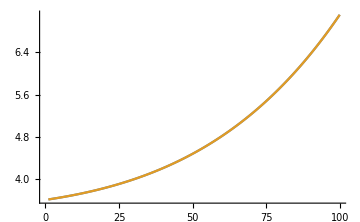

```mathematica
(***Diagnostic Tools***)

(*Parameter History*)
Grid[debugParams[[-10;;-1]]];
Column[eFunc @@ #&/@ debugParams[[-10;;-1]]];
Grid[gFunc @@ #&/@ debugParams[[-10;;-1]]];

(*"Best Parameters" Generated with NMinimize*)
AutoParams=params/.NMinimize[eFunc @@ params,params][[2]];

(*Compare current data, auto-fitted data, and generated data*)
ListPlot[{
(*(Fitfunction@@Prepend[iterParams,#])&/@SamplingSet,*)
(Fitfunction@@Prepend[AutoParams,#])&/@SamplingSet,
Data},Joined->True,ImageSize->Medium]
```

1.5

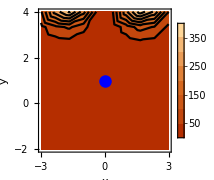
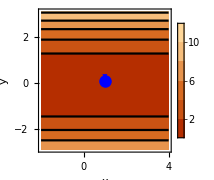
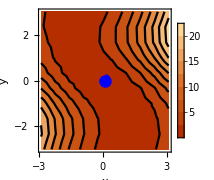

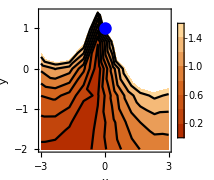
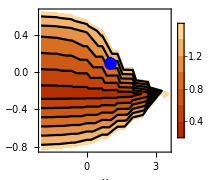
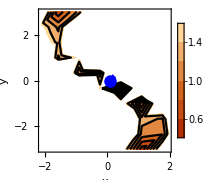

```mathematica
dispGradientRange=3.;
dispGradientThresh=1.5
{displayGradient[1,2],displayGradient[2,3],displayGradient[3,1]}
{displayGradientNorm[1,2,dispGradientThresh],displayGradientNorm[2,3,dispGradientThresh],displayGradientNorm[3,1,dispGradientThresh]}
```

```mathematica
LinePlot[debugParams,Length@debugParams,Length@debugParams]
```

-Graphics3D-

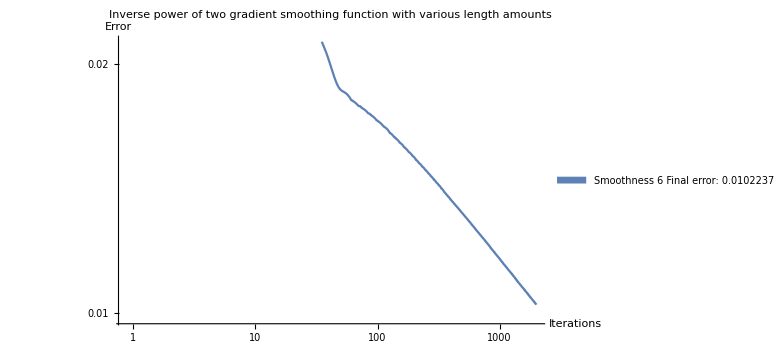

```mathematica
ListLogLogPlot[
Table[RecordedComparisonData[[sm,2]],{sm,1,Length@RecordedComparisonData}],PlotLegends->SwatchLegend[
Table[
Column[{
ToSpacedString@RecordedComparisonData[[sm,1]],
ToSpacedString@{"Final error:",Last@RecordedComparisonData[[sm,2]]}}
],{sm,1,Length@RecordedComparisonData}],
LegendFunction->"Panel"],
PlotLabel->"Inverse power of two gradient smoothing function with various length amounts",
AxesLabel->{"Iterations","Error"},
ImageSize->Large,Joined->True]
```

```mathematica
ListPlot[
Table[{RecordedComparisonData[[sm,1,1]],RecordedComparisonData[[sm,4]]/1000.},{sm,1,Length@RecordedComparisonData}],
AxesLabel->{"Length of smoothing function","Corrections / Iterations"},
PlotLabel->"Correction Amounts of P2 Smoothing Function with various length amounts",
ImageSize->Large
]
```

-Graphics-

```mathematica
Data
TrueParams
```

{-0.000455965,-0.000452736,-0.000448879,-0.000444309,-0.000438932,-0.000432641,-0.00042532,-0.000416842,-0.000407067,-0.00039584,-0.000382993,-0.000368343,-0.000351689,-0.000332816,-0.000311488,-0.000287452,-0.000260435,-0.000230144,-0.000196266,-0.000158465,-0.000116386,-0.0000696518,-0.0000178661,0.0000393888,0.000102548,0.000172065,0.000248407,0.000332052,0.000423487,0.000523202,0.000631683,0.000749408,0.000876835,0.00101439,0.00116248,0.00132142,0.00149148,0.00167284,0.00186556,0.00206957,0.00228464,0.00251032,0.00274594,0.00299055,0.00324288,0.00350126,0.00376359,0.00402725,0.00428905,0.00454511,0.00479077,0.00502051,0.00522782,0.00540503,0.00554323,0.00563207,0.00565958,0.00561201,0.00547358,0.00522629,0.00484964,0.00432036,0.00361213,0.00269524,0.00153628,0.0000977374,-0.0016624,-0.00379104,-0.00634046,-0.00936878,-0.0129405,-0.0171269,-0.0220067,-0.0276669,-0.0342028,-0.041719,-0.0503301,-0.060161,-0.0713479,-0.0840388,-0.0983938,-0.114586,-0.132803,-0.153245,-0.176126,-0.201677,-0.230142,-0.26178,-0.296865,-0.335684,-0.37854,-0.425745,-0.477625,-0.534511,-0.596744,-0.664668,-0.738624,-0.818949,-0.905972,-1.}

{4.73575,9.87798,-8.94354}

```mathematica
First@((
hFunc=paramh/._[vars__]:>Function[{vars},Evaluate@Grad[gFunc@@params,params]];
)//AbsoluteTiming)
```

0.0218398

0.00655904